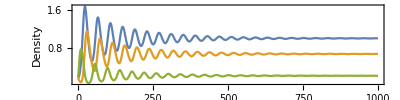

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,T_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t])*R[t] ,
F[0]==0.16,H[0]==0.16,R[0]==0.16},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{α=0.5,λ=0.2,σ=0.3,ρ=0.3,β=0.2,μ=0.3,T=1000},
Traj=Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T] ];
Plot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","Density"},PlotLegends->{"R","H","F"}]
]
```

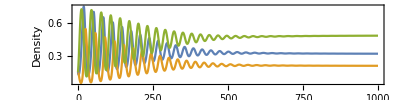
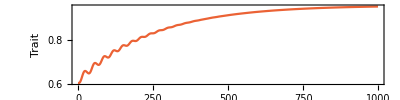
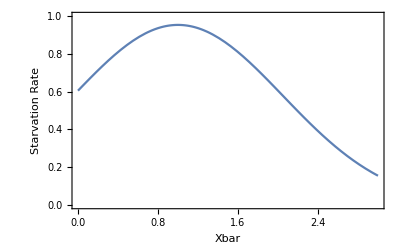

```mathematica
MetapopDyn[α_,λ_,ρ_,β_,μ_,T_,sigmax_,slope_,var_,θ_,varG_] :=(
(*sigma= (sigmax*slope)/(√(var+slope^2))*Exp[(-(xbar[t]-θ)^2)/(2*(var+slope^2))];
Wbar = λ+sigma *(1-R[t])*(F[t]/H[t]-1)+ρ*R[t]*(H[t]/F[t]-R[t]);*)
NDSolve[{
F'[t] ==λ*F[t]-((sigmax*slope)/(√(var+slope^2))*Exp[(-(xbar[t]-θ)^2)/(2*(var+slope^2))])*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==((sigmax*slope)/(√(var+slope^2))*Exp[(-(xbar[t]-θ)^2)/(2*(var+slope^2))])*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t])*R[t] ,
xbar'[t] == varG*D[ λ+( (sigmax*slope)/(√(var+slope^2))*Exp[(-(xbar[t]-θ)^2)/(2*(var+slope^2))] )*(1-R[t])*(F[t]/H[t]-1)+ρ*R[t]*(H[t]/F[t]-R[t]),xbar[t]],
F[0]==0.16,H[0]==0.16,R[0]==0.16,xbar[0]==2},{F,H,R,xbar},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All]);

With[{α=0.5,λ=0.2,ρ=0.9,β=0.2,μ=0.3,T=1000,sigmax=1,slope=1,var=0.1,θ=1,varG=0.01},
Traj=Evaluate[{F[t],H[t],R[t],xbar[t]}/.MetapopDyn[α,λ,ρ,β,μ,T,sigmax,slope,var,θ,varG] ];
Column[{
Legended[
Show[
Table[
Plot[Traj[[1]][[i]],{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","Density"},PlotStyle->ColorData[97,i]],{i,1,3}],ImageSize->400
],SwatchLegend[{ColorData[97,1],ColorData[97,2],ColorData[97,3]},{"R","H","F"}]],

(*Plot[Traj[[1]][[4]],{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","Trait"},PlotStyle->ColorData[97,4],ImageSize->400],*)
Plot[(sigmax*slope)/(√(var+slope^2))*Exp[(-(Traj[[1]][[4]]-θ)^2)/(2*(var+slope^2))],{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","Trait"},PlotStyle->ColorData[97,4],ImageSize->400],

Plot[(sigmax*slope)/(√(var+slope^2))*Exp[(-(xbar-θ)^2)/(2*(var+slope^2))],{xbar,0,3},Frame->True,FrameLabel->{"Xbar","Starvation Rate"},PlotRange->{0,sigmax}]
}]
]
```